```mathematica
(*Множество выпуклой оболочки*)
convexHull ={};

(*Находим с какой стороны находится точка p относительно линии, соединяющей точки p1 и p2*)
findSide[p1_, p2_, p_]:=(
val = ((p[[2]]-p1[[2]])*(p2[[1]]-p1[[1]])-(p2[[2]]-p1[[2]])*(p[[1]]-p1[[1]]));
If[val>0, Return[1]];
If[val<0, Return[-1]];
Return[0];
)

(*Находим расстояние между точкой p и линией соединяющей точки p1 и p2*)
distance[p1_, p2_, p_] := (
Return[Abs[((p[[2]]-p1[[2]])*(p2[[1]]-p1[[1]])-(p2[[2]]-p1[[2]])*(p[[1]]-p1[[1]]))]
]
)

(*алгоритм Quick Hull*)
quickHull[P_, p1_, p2_, side_]:=(Module[{
index = -1,
maxDistance = 0
},
(*Находим точку находящуюся на максимальном расстоянии от прямой p1p2 с указанной стороной*)
For[iQH=1, iQH≤Length[P], iQH++,
temp = distance[p1, p2, P[[iQH]]];
If[(findSide[p1, p2, P[[iQH]]]==side && temp>maxDistance),
index = iQH;
maxDistance = temp;
];
];

(*Если точка не найдена, то добавляем конечные точки p1 и p2 в множество выпуклой оболочки*)
If[index == -1,
AppendTo[convexHull, p1];
AppendTo[convexHull, p2];
Return[Null]
];
(*Запускаем рекурсию*)
quickHull[P,P[[index]], p1, -findSide[P[[index]], p1, p2]];

quickHull[P,P[[index]], p2, -findSide[P[[index]], p2, p1]];
]
)

(*формирование выпуклой оболочки*)
buildHull[P_]:=(

If[Length[P]<3,
Print["Выпуклая оболочка не существует"];
Return[Null];
];

(*Находим точку с максимальной и минимальной x-координатой*)
xMax = 1;
xMin =1;
For[kPH=2, kPH≤Length[P], kPH++,
If[P[[kPH]][[1]]<P[[xMin]][[1]],
xMin = kPH;
];
If[P[[kPH]][[1]] > P[[xMax]][[1]],
xMax = kPH;
]
];
(*Рекурсивно находим выпуклую оболочку с правой стороны линии P[[xMin]]P[[xMax]]*)
quickHull[P, P[[xMin]], P[[xMax]], 1];

(*Рекурсивно находим точки выпуклой оболочки с левой стороны линии P[[xMin]]P[[xMax]]*)
quickHull[P, P[[xMin]], P[[xMax]], -1];
);
(*общий коэффициент для многоугольника (для сортировки точек оболочки по или против часовой стрелки)*)
calcKoef0[P_]:=(
Return[If[Det[({{P[[3]][[1]]-P[[1]][[1]], P[[3]][[2]]-P[[1]][[2]]}, {P[[2]][[1]]-P[[1]][[1]], P[[2]][[2]]-P[[1]][[2]]}})]>0,-1,1]]
)
(*коэффицент для угла между векторами р1р2 и р2р3 (для сортировки точек оболочки по или против часовой стрелки)*)
calcKoef[p1_,p2_,p3_]:=(
Return[If[Det[({{p3[[1]]-p1[[1]], p3[[2]]-p1[[2]]}, {p2[[1]]-p1[[1]], p2[[2]]-p1[[2]]}})]>0,-1,1]]
)

(*периметр оболочки*)
Perimetr[P_]:=(Module[{
perim=0,
i=0
},
For[i=1,i<Length[P],i++,
perim+=EuclideanDistance[P[[i]],P[[Mod[i,Length[P]]+1]]];
];
Return[perim];
])

(*MAIN*)
(*количество точек*)
numOfPoints=20;
(*множество точек*)
arrPoints={};
(*вертикальные габариты поля и границ*)
Hei=50;
(*горизонтальные габариты поля и границ*)
Wid=50;
(*коэфициент скорости точек*)
v=0.5;
(*множество векторов точек*)
V={};
(*запись начальных координат точек*)
For[i=1,i≤numOfPoints,i++,
AppendTo[arrPoints,{RandomChoice[Range[-Hei,Hei]],RandomChoice[Range[-Wid,Wid]]}];
]
arrPoints
(*начальные векторы движения*)
For[i =1,i≤numOfPoints, i++,
AppendTo[V,{v*Cos[RandomReal[{0,2π}]],v*Sin[RandomReal[{0,2π}]]}]
]
V
(*число кадров*)
numOfShots=500;
(*базовая рамка анимации*)
GR1:=Graphics[{
PlotLabel->info,
},
PlotRange->{{-Hei*2,Hei*2}, {-Wid*2,Wid*2}},Frame->True
]
(*отображение отдельной точки*)
Subscript[GRP, i_]:=Graphics[
{
PointSize[0.015],
Point[arrPoints[[i]]],
Text[i,{arrPoints[[i]][[1]]+3.5,arrPoints[[i]][[2]]+3.5}]
},
PlotRange->{{-Hei*2,Hei*2}, {-Wid*2,Wid*2}},Frame->True
]
(*множество выпуклых оболочек для каждого кадра*)
CHSAr={};
(*отображение выпуклой оболочки отдельного кадра*)
Subscript[GRQH, i_]:=Graphics[
{
PointSize[0.015],
Table[Point[CHSAr[[i]][[ig]]],{ig,1,Length[CHSAr[[i]]]}],
Table[Line[{CHSAr[[i]][[ig2]],CHSAr[[i]][[Mod[ig2,Length[CHSAr[[i]]]]+1]]}],{ig2,1,Length[CHSAr[[i]]]}]
},
PlotRange->{{-Hei*2,Hei*2}, {-Wid*2,Wid*2}},Frame->True
]
(*крайнее значение периметра*)
S=300;
(*построение анимации*)
For[i=1,i≤numOfShots,i++,
(*перемещение точек*)
arrPoints+=V;
(*вычисление оболочки*)
buildHull[arrPoints];
CH = DeleteDuplicates[convexHull];
CHS=CH;
(*упорядочивание точек оболочки*)
For[k=1,k≤Length[CHS]-2,k++,
For[l=k+3,l≤Length[CHS],l++,
If[
calcKoef[CHS[[1]],CHS[[2]],CHS[[3]]]*calcKoef0[CHS]*
VectorAngle[CHS[[k+1]]-CHS[[k]],CHS[[k+2]]-CHS[[k+1]]]>
calcKoef[CHS[[1]],CHS[[2]],CHS[[3]]]*calcKoef0[CHS]*
VectorAngle[CHS[[k+1]]-CHS[[k]],CHS[[l]]-CHS[[k+1]]]||(calcKoef[CHS[[1]],CHS[[2]],CHS[[3]]]*calcKoef0[CHS]*
VectorAngle[CHS[[k+1]]-CHS[[k]],CHS[[k+2]]-CHS[[k+1]]]==
calcKoef[CHS[[1]],CHS[[2]],CHS[[3]]]*calcKoef0[CHS]*
VectorAngle[CHS[[k+1]]-CHS[[k]],CHS[[l]]-CHS[[k+1]]]&&EuclideanDistance[CHS[[k+1]],CHS[[k+2]]]>EuclideanDistance[CHS[[k+1]],CHS[[l]]])
,
{CHS[[k+2]],CHS[[l]]}={CHS[[l]],CHS[[k+2]]};
]
]
];
(*запись координат выпуклой оболочки*)
AppendTo[CHSAr,CHS];
(*запись кадра*)
For[j=1,j≤numOfPoints,j++,
If[j==1,Subscript[GR2, i]={Subscript[GRP, j]},Subscript[GR2, i]=Union[Subscript[GR2, i],{Subscript[GRP, j]}]]
];
(*разворот точек*)
If[Perimetr[CHS]>=S,
Subscript[GR2, i]=Union[Subscript[GR2, i],{Subscript[GRQH, i]}];
V*=-1;
];
(*очистка множества выпуклой оболочки*)
convexHull={};
]
ListAnimate[Table[Show[GR1,Subscript[GR2, i]],{i,1,numOfShots}],AnimationRate->7]
```

{{12,-34},{-23,18},{-41,48},{-36,23},{10,-27},{-3,-12},{39,4},{-45,-7},{40,46},{-14,45},{-12,3},{9,-24},{-2,-4},{-19,-22},{28,-8},{-12,15},{-31,-50},{48,-9},{22,-8},{-8,-40}}

{{0.497405,-0.277383},{0.138943,-0.0688112},{0.310798,-0.307399},{0.367745,0.232065},{-0.284131,-0.1361},{-0.493692,0.499999},{0.0587261,-0.446924},{0.289681,0.158096},{-0.33222,0.34524},{-0.491627,-0.138537},{0.0458711,-0.208305},{0.499069,-0.381933},{0.307861,-0.477252},{0.496067,-0.160243},{0.0908625,0.449229},{-0.485092,0.128347},{-0.487553,-0.287593},{0.446379,-0.499294},{0.440326,0.391821},{0.294322,0.190215}}

```mathematica
p1test={-1,5};
p2test={1,5};
p3test={-5,-3};
atest=p2test-p1test
btest=p3test-p2test
angleForFirst[p1test,p2test,p3test]
```

{2,0}

{-6,-8}

ArcCos[-3/5]

{4,4}

```mathematica
Range[-5,5]
RandomChoice[Range[-5,5]]
Show[Line[{1,1},{2,2}]]
```

{-5,-4,-3,-2,-1,0,1,2,3,4,5}

-3

Show::gtype: Line is not a type of graphics.

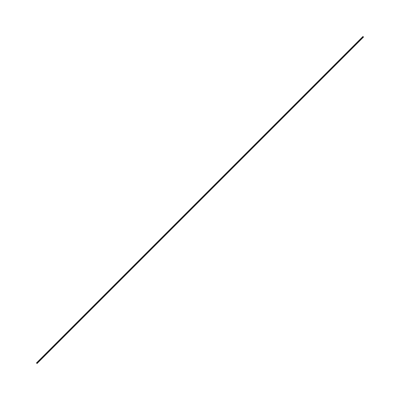

```mathematica
Graphics[Line[{{1,1},{2,2}}]]
```

```mathematica
findSide[{1,1},{2,2},{1.5,1.5}]
```

0

```mathematica
VectorAngle[{2,0},{2,1}]
```

ArcCos[2/(√5)]